InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

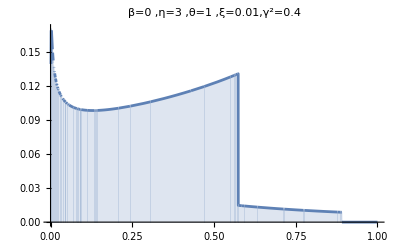

```mathematica
ClearAll["Global`*"]
(*Global parameters case β=0*)
η=3;
θ=1;
γsquare= 0.4;
β=0;
ξ=0.01;
eps = 10^-16;
Which[ 
-γsquare<ξ<=0,
{ν=θ/η;
κ=γsquare-Abs[ξ];
m1=1/κ;
m2=Abs[ξ]/κ;
n1=γsquare-1;
n2=Abs[ξ];
ω=η;},
0<ξ<=1-γsquare,
{ν=θ/η;
κ=γsquare;
m1=1/κ;
m2=(ξ θ)/(κ η);
n1=0;
n2=1-γsquare -ξ;
ω=η;},
1-γsquare<ξ<1,
{ν=η/θ;
κ=1-ξ;
m1=1/κ;
m2=ξ/κ;
n1=1-γsquare -ξ;
n2=0;
ω=θ;}
];
(* Final part for plots*)
m1tilde=m1(n2-n1);
s0=(1+m1tilde)/(ν(1+m2));
c0=((m1tilde ν+ν+m2)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν+1))/(m2+1);

c1=(ν*(m1tilde+1)*((m2+1)/(m1tilde ν+ν+m2+1))^(1/ν-1))/(m1tilde ν+ν+m2+1)^2;
J[s_] = (c0+c1* s)((1+s)/s)^(1/ν);
II[s_]=InverseFunction[J][s];
sa=-((ν-1)/(2 ν))-(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
sb=-((ν-1)/(2 ν))+(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
a=Re[J[sa]];
b=Re[J[sb]];
μ[x_]=Abs[((m2+1)*(m1tilde ν+ν+m2+1))/(ν*(m1tilde+1)*π*x)*Im[1/(s0-II[x])]]*Boole[a<=x<=b];

Plot[ω x^(ω-1)μ[x^ω],{x,0,1},PlotRange->{{0,1},Automatic},Filling->Bottom,PlotLabel->Style[",ξ="<>ToString[ξ]<>",γ^2="<>ToString[γsquare]",η="<>ToString[η]",θ="<>ToString[θ]"β="<>ToString[β],FontSize->22,Black]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

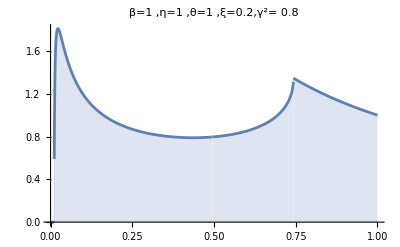

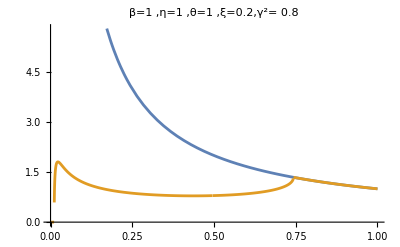

```mathematica
(*Global parameters case β>0*)
ClearAll["Global`*"]
η=1;
θ=1;
γsquare= 0.8;
βtilde=1/η;
β= βtilde* η;
ξ=1-γsquare;
eps = 10^-16;
ν=θ/η;
κ=γsquare;
m1=0;
m2=(ξ θ)/(κ η);
Subscript[m, 2]=m2;
n1=0;
n2=1-γsquare -ξ;
ω=η;
c0=ⅇ^(-(β (1+Subscript[m, 2]))/ν) (-1+ⅇ^(β (1+Subscript[m, 2])))^(2/ν) (-1+ⅇ^(β (1+ν+Subscript[m, 2])))^(-(2+ν)/ν) (-ⅇ^((β (1+ν+Subscript[m, 2]))/ν) ((-1+ⅇ^(β (1+ν+Subscript[m, 2])))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν)+ⅇ^(β (1+ν+Subscript[m, 2])) ((ⅇ^(β (1+Subscript[m, 2])) (-1+ⅇ^(β (1+ν+Subscript[m, 2]))))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν));
c1=-ⅇ^(-(β (1+Subscript[m, 2]))/ν) (-1+ⅇ^(β (1+Subscript[m, 2])))^(-1+2/ν) (ⅇ^(β (1+Subscript[m, 2]))-ⅇ^(β (1+ν+Subscript[m, 2]))) (-1+ⅇ^(β (1+ν+Subscript[m, 2])))^(-(2+ν)/ν) (ⅇ^((β (1+ν+Subscript[m, 2]))/ν) ((-1+ⅇ^(β (1+ν+Subscript[m, 2])))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν)-((ⅇ^(β (1+Subscript[m, 2])) (-1+ⅇ^(β (1+ν+Subscript[m, 2]))))/(-1+ⅇ^(β (1+Subscript[m, 2]))))^(1/ν));
I11=(ⅇ^(β (1+ν+Subscript[m, 2])) (-1+ⅇ^(β (1+Subscript[m, 2]))))/(-ⅇ^(β (1+Subscript[m, 2]))+ⅇ^(β (1+ν+Subscript[m, 2])));
I21=-(1-ⅇ^(β (1+Subscript[m, 2])))/(-ⅇ^(β (1+Subscript[m, 2]))+ⅇ^(β (1+ν+Subscript[m, 2])));
J[s_] = (c0+c1* s)((1+s)/s)^(1/ν);
II[s_]=InverseFunction[J][s];
sa=-((ν-1)/(2 ν))-(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
sb=-((ν-1)/(2 ν))+(1/(2 ν c1))*Sqrt[4 c0 c1 ν+c1^2 (ν-1)^2];
a=Re[J[sa]];
b=Re[J[sb]];
μ[x_]= 1/(π β x)Abs[Arg[I11-II[x]] - Arg[I21 - II[x]]]*Boole[a<=x<=1];
Plot[ω x^(ω-1)μ[x^ω],{x,0,1},PlotRange->{{0,1},Automatic},Filling->Bottom,PlotLabel->Style[",ξ="<>ToString[ξ]<>",γ^2= "<>ToString[γsquare]",η="<>ToString[η]",θ="<>ToString[θ]"β="<>ToString[βtilde],FontSize->22,Black]]
Plot[{1/(βtilde x),ω x^(ω-1)μ[x^ω]},{x,0,1},PlotRange->{{0,1},Automatic},PlotLabel->Style[",ξ="<>ToString[ξ]<>",γ^2= "<>ToString[γsquare]",η="<>ToString[η]",θ="<>ToString[θ]"β="<>ToString[βtilde],FontSize->22,Black]]
```